```mathematica
a=3 
Psipartial[x_,N_] = Sum[2*Sqrt[2]/((2n+1)*Pi)*Sqrt[2/a]*Sin[(2*n+1)*Pi*x/a],{n,0,N}]
Manipulate[Plot[Psipartial[x,Nx],{x,0,a}],{Nx,1,400}]
Psi[x_] = Sum[2*Sqrt[2]/((2n+1)*Pi)*Sqrt[2/a]*Sin[(2*n+1)*Pi*x/a],{n,0,Infinity}]
Plot[Psi[x],{x,0,a}]
Integrate[Psi[x]^2,{x,0,a}]
```

3

1/(√3 π)ⅈ ⅇ^(-ⅈ π x) (2 ⅇ^(ⅈ π x) ArcTanh[ⅇ^(-1/3 ⅈ π x)]-2 ⅇ^(ⅈ π x) ArcTanh[ⅇ^((ⅈ π x)/3)]-(ⅇ^(-2/3 ⅈ π x))^N LerchPhi[ⅇ^(-2/3 ⅈ π x),1,3/2+N]+ⅇ^(2 ⅈ π x) (ⅇ^((2 ⅈ π x)/3))^N LerchPhi[ⅇ^((2 ⅈ π x)/3),1,3/2+N])

(2 ⅈ (ArcTanh[ⅇ^(-1/3 ⅈ π x)]-ArcTanh[ⅇ^((ⅈ π x)/3)]))/(√3 π)

-Graphics-

1

```mathematica
Integrate[Sin[2Pi*x/b]^2*Cos[Pi*x/b]^2,{x,0,b}]
```

b/4

```mathematica
Integrate[Sin[2Pi*x/b]*Cos[Pi*x/b]*Sin[n*Pi*x/b],{x,0,b}]
```

-(2 b (-3+n^2) Sin[n π])/((9-10 n^2+n^4) π)

```mathematica
Integrate[Sin[Pi*x/b]^2,{x,0,b}]
```

b/2

```mathematica
Integrate[Sin[3*Pi*x/b]^2,{x,0,b}]
```

b/2

```mathematica
Integrate[(Sin[Pi*x/b]^2 + Sin[Pi*x*3/b]^2),{x,0,b}]
```

b

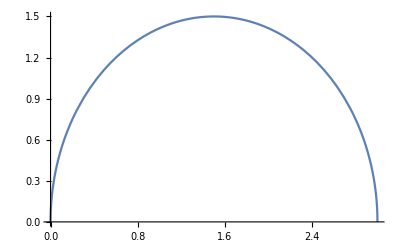

```mathematica
Plot[Sqrt[x(a-x)],{x,0,a}]
```

```mathematica
Integrate[Sin[n*Pi*x/b]Sqrt[x(b-x)],{x,0,b}]
```

∫_0^b √((b-x) x) Sin[(n π x)/b]ⅆx

```mathematica
f[x_] = A(E^(l*x)-1)(E^(l(b-x))-1)
```

A (-1+ⅇ^(l (b-x))) (-1+ⅇ^(l x))

```mathematica
Integrate[f[x]^2,{x,0,b}]
```

(2 A^2 ⅇ^(b l) (2 b l+b l Cosh[b l]-3 Sinh[b l]))/l

```mathematica
Integrate[f[x]*Sin[Pi*x*n/b],{x,0,b}]
```

-(A b^2 l (-b (1+ⅇ^(b l)) l+b (1+ⅇ^(b l)) l Cos[n π]+(-1+ⅇ^(b l)) n π Sin[n π]))/(b^2 l^2 n π+n^3 π^3)